## Máquinas de Estado Finito Y Autómatas

```mathematica
<<VilCretas`
```

```mathematica
(* Modelo para representar el funcionamiento de un ordenador con una memoria primitiva *)
```

```mathematica
(* Simular el comportamiento de un ordenador por ejemplo: para relizar una operacion aritmetica, o hasta realizar un compilador *)
```

```mathematica
(* En un circuito combinatorio no toma en cuenta el factor de la memoria para realizar las salidas, a diferencia de las maquinas de estado finito *)
```

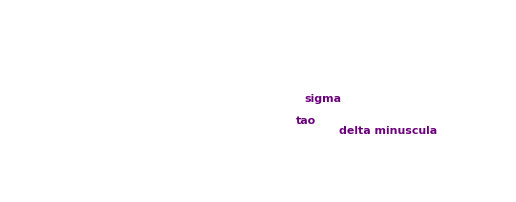
```mathematica
-Graphics--Graphics-
```

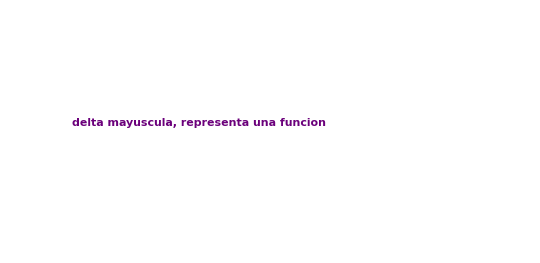
```mathematica
-Graphics--Graphics-
```

```mathematica
(* La función de transición de estados permite ir viendo cómo va cambiando la memoria del ordenador *)
(* La función omega, permite poder devolver las salidas que produce la máquina *)
```

```mathematica
(* Sigma-> Conjunto de estados de la maquina de estado finito, representa como puede ir cambiando la memoria de la computadora *)

(* Tao-> conjunto de símbolos, un abecedario o alfabeto, representa los caractéres que mi computadora va a poder leer o entender,por eso se le llama conjunto de símbolos de entrada *)
```

```mathematica
(* Delta-> símbolos que la máquina está en capacidad de devolver como salida, son la respuesta del sistema, por eso se le llama conjunto de símbolos de salida *)
```

```mathematica
(* Sigma asterísco (es un elemento de sigma)  ->  Es el estado incial de la máquina, el estado del cual parte la máquina, como inicio *)
```

```mathematica
(* Funciones, comparte que el dominio es que el prod cartesiano entre sigma y tao: *)
```

```mathematica
(* Delta mayúscula -> es una funci.08ón que permite ver como el ordenador va cambiando las condiciones en la memoria para responder *)
```

```mathematica
(* Omega -> da como resultado una hilera de salidas, cuando se esta procesando una hilera de símbolos de entrada *)
```

```mathematica
(*-------------------------------------------------------------------------------------------*)
```

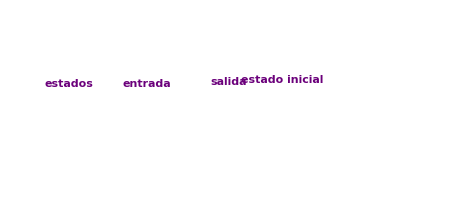
```mathematica
-Graphics--Graphics-
```

```mathematica
(* Diagrama de transicion de la máquina(su recorrido siempre sera unico): *)
(* Toma como nodos los estados de la máquina *)
(* Por cada simbolo de entrada hay una arista con cada estado *)
(* O sea, que por cada estado hay una arista saliente con a y con b *)
(* En un sentido no estricto este es un digrafo *)
```

```mathematica
PC[{Subscript[σ, 0],Subscript[σ, 1],Subscript[σ, 2]},{a,b}]
```

{{σ_0,a},{σ_0,b},{σ_1,a},{σ_1,b},{σ_2,a},{σ_2,b}}

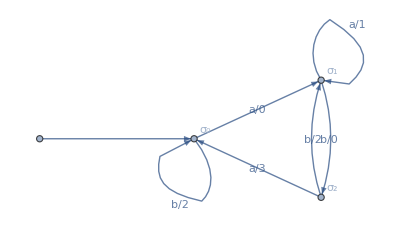

```mathematica
MaquinaToDiagrama[{Subscript[σ, 0],Subscript[σ, 1],Subscript[σ, 2]},{a,b},{0,1,2,3},Subscript[σ, 0],{{Subscript[σ, 0],a,Subscript[σ, 1],0},{Subscript[σ, 0],b,Subscript[σ, 0],2},{Subscript[σ, 1],a,Subscript[σ, 1],1},{Subscript[σ, 1],b,Subscript[σ, 2],0},{Subscript[σ, 2],a,Subscript[σ, 0],3},{Subscript[σ, 2],b,Subscript[σ, 1],2}}]
```

```mathematica
(*-------------------------------------------------------------------------*)
```

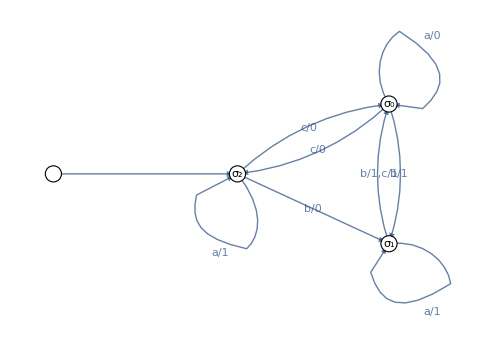

```mathematica
MaquinaToDiagrama[{Subscript[σ, 0],Subscript[σ, 1],Subscript[σ, 2]},{a,b,c},{0,1},Subscript[σ, 2],{{Subscript[σ, 0],a,Subscript[σ, 0],0},{Subscript[σ, 0],b,Subscript[σ, 1],1},{Subscript[σ, 0],c,Subscript[σ, 2],0},{Subscript[σ, 1],a,Subscript[σ, 1],1},{Subscript[σ, 1],b,Subscript[σ, 0],1},{Subscript[σ, 1],c,Subscript[σ, 0],1},{Subscript[σ, 2],a,Subscript[σ, 2],1},{Subscript[σ, 2],b,Subscript[σ, 1],0},{Subscript[σ, 2],c,Subscript[σ, 0],0}},shape->True,radio->0.05]
```

```mathematica
(*---------------------------------------------------------------------------*)
```

```mathematica
(* Extraer los componentes a traves del digrama *)
```

```mathematica
DiagramaToMaquina[]
```

```mathematica
(* Toda hilera siempre se va a poder procesar en una máquina de estado finito, y ese recorrido siempre será único *)
```

```mathematica
(*--------------------------------------------------------------------------------*)
```

```mathematica
(* Hileras de simbolos de entrada: *)
```

```mathematica
(* Se va recorriendo la hilera, viendo las entradas, y posicionandose en el diagrama de transicion *)
```

```mathematica
(* Recordar: Siempre escribir la hilera como un vector *)
```

```mathematica
alfa={a,a,b,b,a,c,c,c,a,a,b,b,c,b,a};
```

```mathematica
(* Con trace, se puede ir viendo cómo se van visitando los estados *)
```

```mathematica
StringSalida[{Subscript[σ, 0],Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3]},{a,b,c},{0,1,2},Subscript[σ, 1],{{Subscript[σ, 0],a,Subscript[σ, 1],1},{Subscript[σ, 0],b,Subscript[σ, 0],1},{Subscript[σ, 0],c,Subscript[σ, 2],2},{Subscript[σ, 1],a,Subscript[σ, 0],2},{Subscript[σ, 1],b,Subscript[σ, 2],0},{Subscript[σ, 1],c,Subscript[σ, 3],0},{Subscript[σ, 2],a,Subscript[σ, 3],1},{Subscript[σ, 2],b,Subscript[σ, 2],0},{Subscript[σ, 2],c,Subscript[σ, 1],1},{Subscript[σ, 3],a,Subscript[σ, 1],2},{Subscript[σ, 3],b,Subscript[σ, 3],2},{Subscript[σ, 3],c,Subscript[σ, 0],2}},alfa,trace->True]
```

{{2,1,0,0,1,2,2,1,2,1,0,0,1,0,1},{σ_1,σ_0,σ_1,σ_2,σ_2,σ_3,σ_0,σ_2,σ_1,σ_0,σ_1,σ_2,σ_2,σ_1,σ_2,σ_3}}

```mathematica
(*-------------------------------------------------------------------------*)
```

```mathematica
(* Con este ejemplo se puede observar que al cambiar la memoria, la salida cambia, el vector de salida con sigma sub 0 no es igual a de sigma sub 1 y asi sucesivamente *)
```

```mathematica
α={a,a,b,b,a,c,c,c,a,a,b,b,c,b,a};
Table[Subscript[σ, j]->StringSalida[{Subscript[σ, 0],Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3]},{a,b,c},{0,1,2},Subscript[σ, j],{{Subscript[σ, 0],a,Subscript[σ, 1],1},{Subscript[σ, 0],b,Subscript[σ, 0],1},{Subscript[σ, 0],c,Subscript[σ, 2],2},{Subscript[σ, 1],a,Subscript[σ, 0],2},{Subscript[σ, 1],b,Subscript[σ, 2],0},{Subscript[σ, 1],c,Subscript[σ, 3],0},{Subscript[σ, 2],a,Subscript[σ, 3],1},{Subscript[σ, 2],b,Subscript[σ, 2],0},{Subscript[σ, 2],c,Subscript[σ, 1],1},{Subscript[σ, 3],a,Subscript[σ, 1],2},{Subscript[σ, 3],b,Subscript[σ, 3],2},{Subscript[σ, 3],c,Subscript[σ, 0],2}},α],{j,{0,1,2,3}}]
```

{σ_0→{1,2,1,1,1,0,2,2,1,2,0,0,1,0,1},σ_1→{2,1,0,0,1,2,2,1,2,1,0,0,1,0,1},σ_2→{1,2,0,0,1,2,2,1,2,1,0,0,1,0,1},σ_3→{2,2,1,1,1,0,2,2,1,2,0,0,1,0,1}}

```mathematica
(* El estado inicial del cual uno parte, tiene un efecto directo en cómo se procesa la hilera, en este caso, es la misma hiler, la misma máquina, pero con solo cambiar el estado inicial, la hilera de símbolos de salida cambia *)
```

```mathematica
(*--------------------------------------------------------------------*)
```

```mathematica
(* Ejemplo 3: *)
```

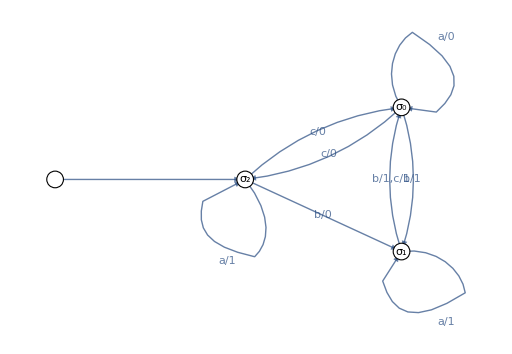

```mathematica
α={c,c,b,b,a,a,b,a,c,c,b,b,a,a,c,b,c,a,b,c};
StringSalida[{Subscript[σ, 0],Subscript[σ, 1],Subscript[σ, 2]},{a,b,c},{0,1},Subscript[σ, 2],{{Subscript[σ, 0],a,Subscript[σ, 0],0},{Subscript[σ, 0],b,Subscript[σ, 1],1},{Subscript[σ, 0],c,Subscript[σ, 2],0},{Subscript[σ, 1],a,Subscript[σ, 1],1},{Subscript[σ, 1],b,Subscript[σ, 0],1},{Subscript[σ, 1],c,Subscript[σ, 0],1},{Subscript[σ, 2],a,Subscript[σ, 2],1},{Subscript[σ, 2],b,Subscript[σ, 1],0},{Subscript[σ, 2],c,Subscript[σ, 0],0}},α]
```

{0,0,0,1,0,0,1,1,1,0,0,1,0,0,0,0,1,0,1,1}

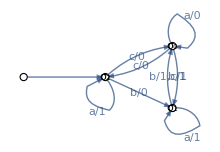
```mathematica
StringSalidaDiagrama[-Graphics-,{c,c,b,b,a,a,b,a,c,c,b,b,a,a,c,b,c,a,b,c}]
```

{0,0,0,1,0,0,1,1,1,0,0,1,0,0,0,0,1,0,1,1}

```mathematica
(* Para que del el conjunto de salida quede todo pegado, para ponerlo en el examen *)
```

```mathematica
StringJoin[ToString/@StringSalida[{Subscript[σ, 0],Subscript[σ, 1],Subscript[σ, 2]},{a,b,c},{0,1},Subscript[σ, 2],{{Subscript[σ, 0],a,Subscript[σ, 0],0},{Subscript[σ, 0],b,Subscript[σ, 1],1},{Subscript[σ, 0],c,Subscript[σ, 2],0},{Subscript[σ, 1],a,Subscript[σ, 1],1},{Subscript[σ, 1],b,Subscript[σ, 0],1},{Subscript[σ, 1],c,Subscript[σ, 0],1},{Subscript[σ, 2],a,Subscript[σ, 2],1},{Subscript[σ, 2],b,Subscript[σ, 1],0},{Subscript[σ, 2],c,Subscript[σ, 0],0}},α]]
```

00010011100100001011

```mathematica
(*-------------------------------------------------------------------*)
```

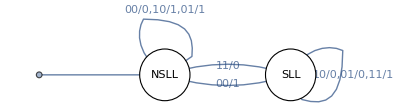

```mathematica
MaquinaSumadoraBinarios[]
```

```mathematica
SumaBinaria[01101111,01110011011,steps->True]
```

-Graphics-

Hilera a procesar en la máquina (intercala los dígitos binarios): {11,11,10,11,01,10,10,01,01,01}

Procesamiento: {{0,1,0,1,0,0,0,0,0,0,1},{NSLL,SLL,SLL,SLL,SLL,SLL,SLL,SLL,SLL,SLL,SLL}}

Se toma la lista de símbolos de salida al revés: {1,0,0,0,0,0,0,1,0,1,0}

10000001010

## Autómatas

```mathematica
(* son maquinas de estado finito con salida 0 y 1. No nos importa la funcion de salida, porque siempre sera 0 o un 1, si es un estado no aceptado, la salida es 1 si es no aceptado es 0  *)
```

```mathematica
(* Esta máquina no es un autómata ya que aunque todas sus entradas son 1 o 0, no cumple con la segunda condición, que es que todas las aristas entrantes a cualquier nodo, deben de tener el mismo símbolo de salida *)
```

```mathematica
(*--------------------------------------------------------------------*)
```

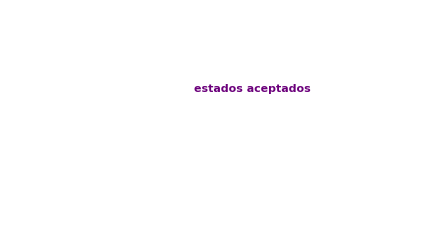
```mathematica
-Graphics--Graphics-
```

```mathematica
(* Los estados aceptados se marcan con dos circulos *)
```

```mathematica
(* Ya no se colocan los simbolos de salida en las aristas *)
```

```mathematica
PC[{Subscript[σ, 0],Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3]},{a,b}]
```

{{σ_0,a},{σ_0,b},{σ_1,a},{σ_1,b},{σ_2,a},{σ_2,b},{σ_3,a},{σ_3,b}}

```mathematica
A=Automata[{Subscript[σ, 0],Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3]},{a,b},Subscript[σ, 2],{{Subscript[σ, 0],a,Subscript[σ, 0]},{Subscript[σ, 0],b,Subscript[σ, 1]},{Subscript[σ, 1],a,Subscript[σ, 2]},{Subscript[σ, 1],b,Subscript[σ, 1]},{Subscript[σ, 2],a,Subscript[σ, 3]},{Subscript[σ, 2],b,Subscript[σ, 1]},{Subscript[σ, 3],a,Subscript[σ, 2]},{Subscript[σ, 3],b,Subscript[σ, 0]}},{Subscript[σ, 0],Subscript[σ, 3]}]
```

```mathematica
(* Si todo sale bien deberia de mostrar este mensaje, si no muestra el mensaje, hay un error en la info pasada*)
```

- Automaton -

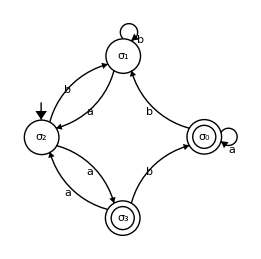

```mathematica
AutomataToDiagrama[A]
```

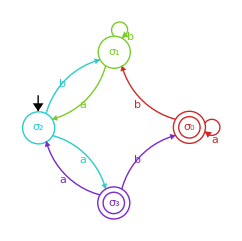

```mathematica
AutomataToDiagrama[A,colores->True]
```

```mathematica
(*-----------------------------------------------*)
```

```mathematica
PC[{Subscript[σ, 0],Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3]},{a,b,c}]
```

{{σ_0,a},{σ_0,b},{σ_0,c},{σ_1,a},{σ_1,b},{σ_1,c},{σ_2,a},{σ_2,b},{σ_2,c},{σ_3,a},{σ_3,b},{σ_3,c}}

- Automaton -

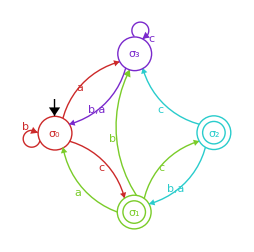

```mathematica
A=Automata[{Subscript[σ, 0],Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3]},{a,b,c},Subscript[σ, 0],{{Subscript[σ, 0],a,Subscript[σ, 3]},{Subscript[σ, 0],b,Subscript[σ, 0]},{Subscript[σ, 0],c,Subscript[σ, 1]},{Subscript[σ, 1],a,Subscript[σ, 0]},{Subscript[σ, 1],b,Subscript[σ, 3]},{Subscript[σ, 1],c,Subscript[σ, 2]},{Subscript[σ, 2],a,Subscript[σ, 1]},{Subscript[σ, 2],b,Subscript[σ, 1]},{Subscript[σ, 2],c,Subscript[σ, 3]},{Subscript[σ, 3],a,Subscript[σ, 0]},{Subscript[σ, 3],b,Subscript[σ, 0]},{Subscript[σ, 3],c,Subscript[σ, 3]}},{Subscript[σ, 1],Subscript[σ, 2]}]

AutomataToDiagrama[A,colores->True]
```

```mathematica
(* Recordar que lo que devuelve este comando no es un grafo, es un dibujo, la variable donde se guarda el resultado del comando si es un grafo o automata *)
```

```mathematica
ComponentesAutomata[A]
```

Estados: {σ_0,σ_1,σ_2,σ_3}

Símbolos de entrada: {a,b,c}

Estado inicial: σ_0

Estados aceptados: {σ_1,σ_2}

(  | a | b | c
σ_0 | σ_3 | σ_0 | σ_1
σ_1 | σ_0 | σ_3 | σ_2
σ_2 | σ_1 | σ_1 | σ_3
σ_3 | σ_0 | σ_0 | σ_3)

Función de transición de estados con otro formato: {{σ_0,a,σ_3},{σ_0,b,σ_0},{σ_0,c,σ_1},{σ_1,a,σ_0},{σ_1,b,σ_3},{σ_1,c,σ_2},{σ_2,a,σ_1},{σ_2,b,σ_1},{σ_2,c,σ_3},{σ_3,a,σ_0},{σ_3,b,σ_0},{σ_3,c,σ_3}}

```mathematica
(*-----------------------------------------------------------------------*)
```

## Hileras en Autómatas

```mathematica
(* En automatas interesa saber si la hilera es aceptada o no, en maquina interesa saber la salida generada por la hilera al recorrer el diagrama *)

(* Para saber si una hilera es aceptada, el ultimo elemento de la hilera debe ser aceptado *)
```

```mathematica
(* Recordar: *)
(* Autómatas determinísticos: 
determinista lo que quiere decir es que siempre se va a poder procesar una hilera y además se procesa de forma única *)

(* Los autómatas no determinísticos no cumplen esto, van haber hileras que no se puedan procesar y otra sí, y además pueden haber múltiples formas de recorrer el diagrama *)
```

```mathematica
(*------------------------------------------------------------------------------*)
```

```mathematica
(* automata deterministico: existe una unica forma de recorrer el diagrama para obtener la hilera *)
```

```mathematica
α={a,b,c,b,b,a,c,c,a,b,c,c,a,b,b};
A1=Automata[{Subscript[σ, 0],Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3]},{a,b,c},Subscript[σ, 0],{{Subscript[σ, 0],a,Subscript[σ, 3]},{Subscript[σ, 0],b,Subscript[σ, 0]},{Subscript[σ, 0],c,Subscript[σ, 1]},{Subscript[σ, 1],a,Subscript[σ, 0]},{Subscript[σ, 1],b,Subscript[σ, 3]},{Subscript[σ, 1],c,Subscript[σ, 2]},{Subscript[σ, 2],a,Subscript[σ, 1]},{Subscript[σ, 2],b,Subscript[σ, 1]},{Subscript[σ, 2],c,Subscript[σ, 3]},{Subscript[σ, 3],a,Subscript[σ, 0]},{Subscript[σ, 3],b,Subscript[σ, 0]},{Subscript[σ, 3],c,Subscript[σ, 3]}},{Subscript[σ, 1],Subscript[σ, 2]}];
StringAceptadaQ[A1,α]
StringAceptadaQ[A1,α,trace->True]
```

False

```mathematica
(* Con trace se puede ver cómo se van visitando los estados *)
```

{False,{σ_0,σ_3,σ_0,σ_1,σ_3,σ_0,σ_3,σ_3,σ_3,σ_0,σ_0,σ_1,σ_2,σ_1,σ_3,σ_0}}

```mathematica
A2=Automata[{Subscript[σ, 0],Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3],Subscript[σ, 4]},{a,b,c},Subscript[σ, 4],{{Subscript[σ, 0],a,Subscript[σ, 0]},{Subscript[σ, 0],b,Subscript[σ, 1]},{Subscript[σ, 0],c,Subscript[σ, 4]},{Subscript[σ, 1],a,Subscript[σ, 1]},{Subscript[σ, 1],b,Subscript[σ, 2]},{Subscript[σ, 1],c,Subscript[σ, 4]},{Subscript[σ, 2],a,Subscript[σ, 2]},{Subscript[σ, 2],b,Subscript[σ, 2]},{Subscript[σ, 2],c,Subscript[σ, 3]},{Subscript[σ, 3],a,Subscript[σ, 4]},{Subscript[σ, 3],b,Subscript[σ, 4]},{Subscript[σ, 3],c,Subscript[σ, 0]},{Subscript[σ, 4],a,Subscript[σ, 4]},{Subscript[σ, 4],b,Subscript[σ, 4]},{Subscript[σ, 4],c,Subscript[σ, 2]}},{Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3]}];
StringAceptadaQ[A2,α]
StringAceptadaQ[A2,α,trace->True]
```

True

{True,{σ_4,σ_4,σ_4,σ_2,σ_2,σ_2,σ_2,σ_3,σ_0,σ_0,σ_1,σ_4,σ_2,σ_2,σ_2,σ_2}}

## Autómatas Equivalentes

```mathematica
(* El lenguaje de un automatas son todas las hileras de simbolos de entrada que el automata acepta, puede ser finito o infinito *)
```

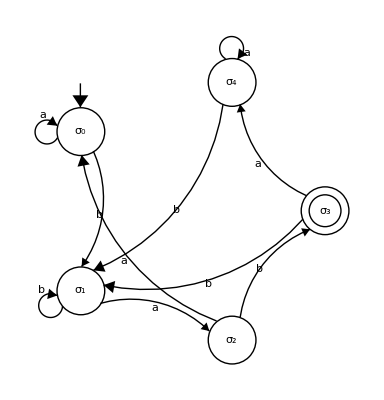

{{b,a,b},{a,b,a,b},{b,b,a,b},{a,a,b,a,b},{a,b,b,a,b},{b,b,b,a,b},{a,a,a,b,a,b},{a,a,b,b,a,b},{a,b,b,b,a,b},{b,a,a,b,a,b},{b,a,b,b,a,b},{b,b,b,b,a,b}}

```mathematica
A=Automata[{Subscript[σ, 0],Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3],Subscript[σ, 4]},{a,b},Subscript[σ, 0],{{Subscript[σ, 0],a,Subscript[σ, 0]},{Subscript[σ, 0],b,Subscript[σ, 1]},{Subscript[σ, 1],a,Subscript[σ, 2]},{Subscript[σ, 1],b,Subscript[σ, 1]},{Subscript[σ, 2],a,Subscript[σ, 0]},{Subscript[σ, 2],b,Subscript[σ, 3]},{Subscript[σ, 3],a,Subscript[σ, 4]},{Subscript[σ, 3],b,Subscript[σ, 1]},{Subscript[σ, 4],a,Subscript[σ, 4]},{Subscript[σ, 4],b,Subscript[σ, 1]}},{Subscript[σ, 3]}];
AutomataToDiagrama[A]
LenguajeStrings[A,6,limite->True]
```

```mathematica
(* Todas terminan con bab *)
```

```mathematica
(* cantidad de hileras aceptadas por el automata que sean menor o igual a 10, si se quita el limite, solo cuenta las hileras de longitud 10 *)
```

```mathematica
LenguajeCantidad[A,10,limite->True]
```

204

```mathematica
(*---------------------------------------------------------------------*)
```

```mathematica
(* usualmente al devolverse, uno se va a estados que tengan los lazos con la entrada que le falte la arista saliente *)
```

```mathematica
(*----------------------------------------------------------------*)
```

```mathematica
(* a diferencia del ejemplo anterior, acá podemos quedarnos enlazados en la arista saliente con b de sigma 1, ya que solo pide que tenga al menos dos letras a  *)
```

```mathematica
(*------------------------------------------------------------*)
```

```mathematica
(* Para saber todas las posibles combinaciones de esas dos a y dos b*)
```

```mathematica
Permutations[{a,a,b,b}]
```

```mathematica
(* todas las hileras que podría aceptar el autómata *)
```

{{a,a,b,b},{a,b,a,b},{a,b,b,a},{b,a,a,b},{b,a,b,a},{b,b,a,a}}

```mathematica
(* Automaticamente queda guardado en una variable G mayuscula, el 2 es porque son 2 de cada letra *)
```

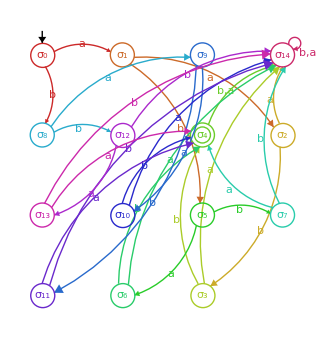

```mathematica
AutomataExactamente[{{a,2},{b,2}},colores->True]
```

```mathematica
ComponentesAutomata[G]
```

Estados: {σ_0,σ_1,σ_2,σ_3,σ_4,σ_5,σ_6,σ_7,σ_8,σ_9,σ_10,σ_11,σ_12,σ_13,σ_14}

Símbolos de entrada: {a,b}

Estado inicial: σ_0

Estados aceptados: {σ_4}

(  | a | b
σ_0 | σ_1 | σ_8
σ_1 | σ_2 | σ_5
σ_2 | σ_14 | σ_3
σ_3 | σ_14 | σ_4
σ_4 | σ_14 | σ_14
σ_5 | σ_6 | σ_7
σ_6 | σ_14 | σ_4
σ_7 | σ_4 | σ_14
σ_8 | σ_9 | σ_12
σ_9 | σ_10 | σ_11
σ_10 | σ_14 | σ_4
σ_11 | σ_4 | σ_14
σ_12 | σ_13 | σ_14
σ_13 | σ_4 | σ_14
σ_14 | σ_14 | σ_14)

Función de transición de estados con otro formato: {{σ_0,a,σ_1},{σ_0,b,σ_8},{σ_1,a,σ_2},{σ_1,b,σ_5},{σ_2,a,σ_14},{σ_2,b,σ_3},{σ_3,a,σ_14},{σ_3,b,σ_4},{σ_4,a,σ_14},{σ_4,b,σ_14},{σ_5,a,σ_6},{σ_5,b,σ_7},{σ_6,a,σ_14},{σ_6,b,σ_4},{σ_7,a,σ_4},{σ_7,b,σ_14},{σ_8,a,σ_9},{σ_8,b,σ_12},{σ_9,a,σ_10},{σ_9,b,σ_11},{σ_10,a,σ_14},{σ_10,b,σ_4},{σ_11,a,σ_4},{σ_11,b,σ_14},{σ_12,a,σ_13},{σ_12,b,σ_14},{σ_13,a,σ_4},{σ_13,b,σ_14},{σ_14,a,σ_14},{σ_14,b,σ_14}}

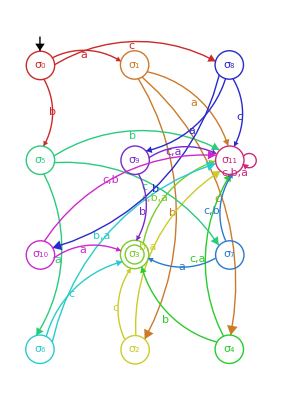

```mathematica
AutomataExactamente[{{a,1},{b,1},{c,1}},colores->True]
```

```mathematica
(*----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------*)
```

## Autómatas No Determinísticos

```mathematica
(* Autómatas que no tiene una única forma de procesar una hilera, pueden ser varias formas, ninguna, o puede ser única *)
```

```mathematica
(* Para saber si un automata es no determinístico, la función de transición de estados, no son imágenes, son conjuntos de estados, incluyendo al conjunto vacío *)
```

```mathematica
(*--------------------------------------------------------------*)
```

```mathematica
(* Observar que no hay una igual cantidad de aristas salientes y entrantes con los símbolos de entrada, a,b,c en este caso *)
(* el conjunto vacío indica que mo hay una arista saliente con esa letra, precisamente esto es lo que causa que no todas las hileras sean procesables *)
```

```mathematica
(* En un automata no deterministico, una hilera es aceptada cuando hay al menos una ruta que termine en un estado aceptado *)
```

```mathematica
(* Una misma hilera puede tener distintas rutas y ser en algunas aceptadas y en otras no *)
```

```mathematica
(*-----------------------------------------------------------------------*)
```

```mathematica
(* Recordar que acá se debe de escribir como conjunto, o sea con llaves adentro también *)
```

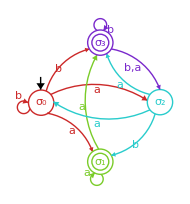

```mathematica
A=Automata[{Subscript[σ, 0],Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3]},{a,b},Subscript[σ, 0],{{Subscript[σ, 0],a,{Subscript[σ, 1],Subscript[σ, 2]}},{Subscript[σ, 0],b,{Subscript[σ, 0],Subscript[σ, 3]}},{Subscript[σ, 1],a,{Subscript[σ, 1],Subscript[σ, 3]}},{Subscript[σ, 1],b,{}},{Subscript[σ, 2],a,{Subscript[σ, 0],Subscript[σ, 3]}},{Subscript[σ, 2],b,{Subscript[σ, 1]}},{Subscript[σ, 3],a,{Subscript[σ, 2]}},{Subscript[σ, 3],b,{Subscript[σ, 2],Subscript[σ, 3]}}},{Subscript[σ, 1],Subscript[σ, 3]}];
AutomataToDiagrama[A,colores->True]
```

```mathematica
(* O también: ToExpression[Characters[ToString[bbaababababa]]]*)
```

```mathematica
Subscript[α, 1]={b,b,a,a,b,a,a,b,a,a,a,a,b,a,a};
Subscript[α, 2]={b,a,b,b,b,b,a,a,a,b,b,a,b,b,b};
Table[StringAceptadaQ[A,hilera],{hilera,{Subscript[α, 1],Subscript[α, 2]}}]
```

{True,False}

```mathematica
(* Es muchísimo más complejo demostrar que una hilera es no aceptada en un autómata no determinístico, ya que habría que contemplar todas las posibles rutas y ver que terminen en estados no aceptados *)

(* Por lo que se tranforma a un autómata det. equivalente, en donde si la hilera termina en un estado no aceptado, ya se sabe que al ser la ruta única, hasta ahí llega el proceso *)
```

## Autómatas Determinísticos Equivalentes

```mathematica
(* Cualquier automata no deterministico, puede ser transformado a un automata deterministico equivalente *)
```

```mathematica
(* 1) los estados del nuevo automata prima corresponde a los estados de automata prima, o sea 2^n *)
```

```mathematica
(* 2) la funcion de conjunto de entrada que tenga vacio va a dar vacio *)
(* 3) los estado aceptados de del automata prima, van a ser los estados que tengan al ruta aceptada del automata no deterministico *)
```

```mathematica
(*-------------------------------------------------------------------*)
```

```mathematica
(* Conjunto potencia, para encontrar los nuevos estados del automata deterministico equivalente *)
```

```mathematica
Subsets[{Subscript[σ, 0],Subscript[σ, 1],Subscript[σ, 2]}]
```

{{},{σ_0},{σ_1},{σ_2},{σ_0,σ_1},{σ_0,σ_2},{σ_1,σ_2},{σ_0,σ_1,σ_2}}

```mathematica
(* se les ponen a cada uno, un nuevo número *)
```

```mathematica
(* los símbolos de entrada van a ser los mismos que el no deterministico *)
```

```mathematica
(* Los estados aceptados van a ser todos los nuevos estados que contengan algún estado aceptado del no deterministico *)
```

```mathematica
(* Ahora, para la función de transición de estados: *)
```

```mathematica
(* Se usa como base, la tabla del no deter. *)
```

```mathematica
(* Tener cuidado cuando ya los nuevos estados están compuestos por más de un estado: *)
```

```mathematica
(* Una estrategia para entender mejor el diagrama, considerando que la cantidad de estados se rigen por la forma 2^n, se utiliza el un diagrama reducido, el cual elimina los estados por los cuales nunca se pasa *)
```

```mathematica
(* se parte desde nuevo estado 1 *)
```

```mathematica
(* en este caso, no se estaria implementando el estado nuevo estado #3, ya que desde el nuevo estado #1 no se visita *)
```

```mathematica
(*--------------------------------------------------------------------------------------------*)
```

```mathematica
(* Primero obtener todos los subconjuntos del conjunto *)
```

```mathematica
Subsets[{Subscript[σ, 0],Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3]}]
```

{{},{σ_0},{σ_1},{σ_2},{σ_3},{σ_0,σ_1},{σ_0,σ_2},{σ_0,σ_3},{σ_1,σ_2},{σ_1,σ_3},{σ_2,σ_3},{σ_0,σ_1,σ_2},{σ_0,σ_1,σ_3},{σ_0,σ_2,σ_3},{σ_1,σ_2,σ_3},{σ_0,σ_1,σ_2,σ_3}}

```mathematica
(* Los simbolos de entrada, siempre corresponden a los simbolos originales dados *)
```

```mathematica
(* función de transición de estados: *)
```

```mathematica
-Graphics--Graphics--Graphics-
```

```mathematica
(* Para hacer el diagrama reducido: *)
```

```mathematica
(*-------------------------------------------------------------------------*)
```

```mathematica
(* Encontrar un automata deterministico equivalente del ejemplo 7.22 *)
```

```mathematica
PC[{Subscript[σ, 0],Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3]},{a,b}]
```

{{σ_0,a},{σ_0,b},{σ_1,a},{σ_1,b},{σ_2,a},{σ_2,b},{σ_3,a},{σ_3,b}}

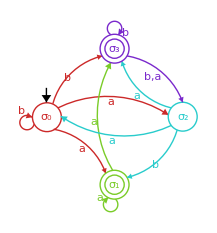

```mathematica
A=Automata[{Subscript[σ, 0],Subscript[σ, 1],Subscript[σ, 2],Subscript[σ, 3]},{a,b},Subscript[σ, 0],{{Subscript[σ, 0],a,{Subscript[σ, 1],Subscript[σ, 2]}},{Subscript[σ, 0],b,{Subscript[σ, 0],Subscript[σ, 3]}},{Subscript[σ, 1],a,{Subscript[σ, 1],Subscript[σ, 3]}},{Subscript[σ, 1],b,{}},{Subscript[σ, 2],a,{Subscript[σ, 0],Subscript[σ, 3]}},{Subscript[σ, 2],b,{Subscript[σ, 1]}},{Subscript[σ, 3],a,{Subscript[σ, 2]}},{Subscript[σ, 3],b,{Subscript[σ, 2],Subscript[σ, 3]}}},{Subscript[σ, 1],Subscript[σ, 3]}];
AutomataToDiagrama[A,colores->True]
```

```mathematica
(* Ahora para encontrar el automata det. equivalente con el comando AutomataDeterministicoEquivalente: *)
```

Diagrama de transición del autómata no determinístico:

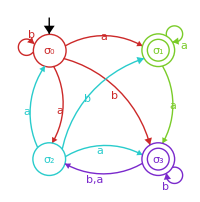

Estados del nuevo autómata:

μ_0={}

μ_1={σ_0}

μ_2={σ_1}

μ_3={σ_2}

μ_4={σ_3}

μ_5={σ_0,σ_1}

μ_6={σ_0,σ_2}

μ_7={σ_0,σ_3}

μ_8={σ_1,σ_2}

μ_9={σ_1,σ_3}

μ_10={σ_2,σ_3}

μ_11={σ_0,σ_1,σ_2}

μ_12={σ_0,σ_1,σ_3}

μ_13={σ_0,σ_2,σ_3}

μ_14={σ_1,σ_2,σ_3}

μ_15={σ_0,σ_1,σ_2,σ_3}

Estado inicial: μ_1

Estados aceptados: {μ_2,μ_4,μ_5,μ_7,μ_8,μ_9,μ_10,μ_11,μ_12,μ_13,μ_14,μ_15}

(  | a | b
μ_0 | μ_0 | μ_0
μ_1 | μ_8 | μ_7
μ_2 | μ_9 | μ_0
μ_3 | μ_7 | μ_2
μ_4 | μ_3 | μ_10
μ_5 | μ_14 | μ_7
μ_6 | μ_15 | μ_12
μ_7 | μ_8 | μ_13
μ_8 | μ_12 | μ_2
μ_9 | μ_14 | μ_10
μ_10 | μ_13 | μ_14
μ_11 | μ_15 | μ_12
μ_12 | μ_14 | μ_13
μ_13 | μ_15 | μ_15
μ_14 | μ_15 | μ_14
μ_15 | μ_15 | μ_15)

Diagrama de transición del nuevo autómata:

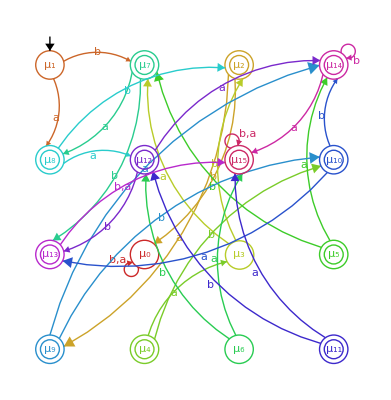

Diagrama de transición reducido del nuevo autómata:

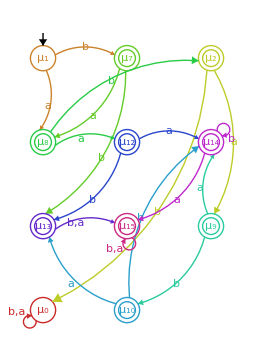

```mathematica
AutomataDeterministicoEquivalente[A,colores->True]
```

```mathematica
(* Con onlyreduce se muestra solo el diagrama del automata equivalente reducido *)
```

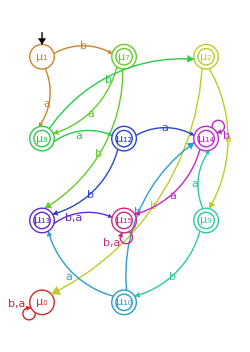

```mathematica
AutomataDeterministicoEquivalente[A,colores->True, onlyreduce->True]
```

```mathematica
(* En G, se guarda automaticamente el automata equivalente reducido, por lo que ahora con este comando se pueden ver sus componentes *)
```

```mathematica
ComponentesAutomata[G]
```

Estados: {μ_0,μ_1,μ_2,μ_7,μ_8,μ_9,μ_10,μ_12,μ_13,μ_14,μ_15}

Símbolos de entrada: {a,b}

Estado inicial: μ_1

Estados aceptados: {μ_2,μ_7,μ_8,μ_9,μ_10,μ_12,μ_13,μ_14,μ_15}

(  | a | b
μ_0 | μ_0 | μ_0
μ_1 | μ_8 | μ_7
μ_2 | μ_9 | μ_0
μ_7 | μ_8 | μ_13
μ_8 | μ_12 | μ_2
μ_9 | μ_14 | μ_10
μ_10 | μ_13 | μ_14
μ_12 | μ_14 | μ_13
μ_13 | μ_15 | μ_15
μ_14 | μ_15 | μ_14
μ_15 | μ_15 | μ_15)

Función de transición de estados con otro formato: {{μ_0,a,μ_0},{μ_0,b,μ_0},{μ_1,a,μ_8},{μ_1,b,μ_7},{μ_2,a,μ_9},{μ_2,b,μ_0},{μ_7,a,μ_8},{μ_7,b,μ_13},{μ_8,a,μ_12},{μ_8,b,μ_2},{μ_9,a,μ_14},{μ_9,b,μ_10},{μ_10,a,μ_13},{μ_10,b,μ_14},{μ_12,a,μ_14},{μ_12,b,μ_13},{μ_13,a,μ_15},{μ_13,b,μ_15},{μ_14,a,μ_15},{μ_14,b,μ_14},{μ_15,a,μ_15},{μ_15,b,μ_15}}